```mathematica
(*TODO: factor the synapse coordinates finder into methods that take in source and target and return the edges desired.*)
f[x_]:=x+1
l[x_]:=StringLength[ToString[x,InputForm]]-1
r3r1[i_,lst_]:=StringPadLeft[ToString[lst[[i]][[1]]],13,"0"]<>StringPadLeft[ToString[lst[[i]][[2]]],13,"0"]<>StringPadLeft[ToString[lst[[i]][[3]]],13,"0"]
r1r3[s_]:={ToExpression[StringTake[s,13]],ToExpression[StringTake[s,{14,26}]],ToExpression[StringTake[s,{27,39}]]}
relabel[dups_,len_]:=(rel=Range[len];Do[Do[rel[[dups[[i]][[j+1]]]]=dups[[i]][[1]],{j,Length[dups[[i]]]-1}],{i,Length[dups]}]) (*go through and assign vertex identities*)
relabel2[dups_,rel_]:=Do[Do[rel[[dups[[i]][[j+1]]]]=dups[[i]][[1]],{j,Length[dups[[i]]]-1}],{i,Length[dups]}]
relabel3[dups_]:=Do[Do[rel[[dups[[i]][[j+1]]]]=dups[[i]][[1]],{j,Length[dups[[i]]]-1}],{i,Length[dups]}]
```

```mathematica
vf1=BinaryReadList["p12v.dat","Real32"];
vf1=ArrayReshape[vf1,{Length[vf1]/3,3}];
ve1=Rationalize[BinaryReadList["p12e.dat","Real32"]];
ve1=ArrayReshape[ve1,{Length[ve1]/2,2}];
ve1=Map[f,ve1];
```

```mathematica
vf2=BinaryReadList["p23v.dat","Real32"];
vf2=ArrayReshape[vf2,{Length[vf2]/3,3}];
ve2=Rationalize[BinaryReadList["p23e.dat","Real32"]];
ve2=ArrayReshape[ve2,{Length[ve2]/2,2}];
ve2
(*ve2=Map[f,ve2];*)
```

{{1,11024},{2,10829},{3,10187},{4,7},{5,12387},{6,4},{7,8},{8,11},{9,14},{10,12},{11,10},{12,15},{13,10},{14,16},{15,19},{16,17},{17,20},{18,21},{19,26},{20,23},{21,25},{22,30},{23,30},{24,22},{25,24},{26,31},15376,{15403,15395},{15404,15399},{15405,15398},{15406,15403},{15407,15405},{15408,15405},{15409,15406},{15410,15406},{15411,15419},{15412,15404},{15413,15408},{15414,15416},{15415,15416},{15416,15417},{15417,15412},{15418,15414},{15419,15414},{15420,15410},{15421,15411},{15422,15420},{15423,15413},{15424,15423},{15425,15424},{15426,15425},{15427,15425}}
 |  |  |  |

```mathematica
vf3=BinaryReadList["p34v.dat","Real32"];
vf3=ArrayReshape[vf3,{Length[vf3]/3,3}];
ve3=Rationalize[BinaryReadList["p34e.dat","Real32"]];
ve3=ArrayReshape[ve3,{Length[ve3]/2,2}];
ve3
(*ve3=Map[f,ve3];*)
```

{{1,30106},{2,30042},{3,29990},{4,29954},{5,29808},{6,29753},{7,27922},{8,29742},{9,30113},{10,29191},{11,28719},{12,28703},{13,28690},{14,28431},{15,28423},{16,28337},{17,29947},{18,30166},{19,29116},{20,28140},{21,29895},{22,44},{23,27320},30188,{30212,30209},{30213,30221},{30214,30221},{30215,30208},{30216,30212},{30217,30215},{30218,30215},{30219,0},{30220,0},{30221,0},{30222,30214},{30223,30198},{30224,30231},{30225,30223},{30226,30225},{30227,28750},{30228,30227},{30229,30226},{30230,30229},{30231,30230},{30232,28167},{30233,29525},{30234,29806}}
 |  |  |  |

```mathematica
stimsites={{768192,201868,158680},{771292,203448,168920},{766144,201048,160600},{766924,191740,169520},{767472,198080,162880},{760524,200544,153440},{787164,222372,169720},{783400,227152,159800},{770868,218780,149880},{766184,215564,147520},{771224,206004,163120},{770868,191584,173720},{771428,203428,168680},{777896,210616,163720},{773688,223512,147440},{773064,221384,152000},{781172,216224,166080},{765248,211352,147360},{770880,203680,165840},{785960,213984,170840},{771836,188048,177760},{776404,207676,165760},{787840,222736,169240},{783624,227712,159960},{770076,201028,164920},{785212,213184,172400},{770216,209760,153440},{778136,214400,159480},{773924,226532,146920},{774988,221220,149600},{774732,213080,159360},{782424,222128,164760},{774504,223616,147480},{772404,211084,162080},{682152,179480,71520},{780576,205528,174760},{761424,200584,153240},{784372,227624,159640},{770776,218024,149560},{779280,219456,161320},{764992,212128,147520},{768120,191000,171600},{770968,203784,166520},{786656,223652,168600},{780216,213840,167000},{760320,200532,153320},{770584,218016,150440},{778256,215292,162040},{765308,215756,146600},{773632,214036,156560},{775300,221592,154160},{765272,197472,164120},{775088,220080,151400},{769152,209036,153760},{773448,216188,157120},{773928,213280,157440},{782036,221568,163880},{764348,212040,146800},{765636,215780,146480},{775888,212868,160640},{768116,196848,165360},{771528,198776,167920},{773272,220436,150680},{767060,191240,170440},{759504,197040,155320},{766252,200976,158600},{776448,207704,165640},{763624,210460,148360},{771060,188864,175560},{772976,220520,150120},{770716,196272,167880},{779924,225704,157280},{780596,203704,175920},{770832,218052,150120},{765800,211136,148560},{775412,220588,151480},{768860,208168,156120},{768576,201100,164160},{780688,205644,174920},{764504,191592,166840},{773328,212904,156440},{773068,223808,152440},{773128,212648,155880},{765624,215852,146360},{783828,215612,171480},{775648,210960,167600},{772772,228000,147360},{767168,191556,169920},{776792,221456,155600},{764152,212780,146560},{770656,205732,160400},{775760,200048,172320},{784480,224948,166160},{765124,211432,146960},{766776,198500,164280},{765320,215852,146800},{768608,207728,156320},{767656,200256,163560},{772408,192296,173080},{775464,200520,170560},{786344,218480,170160},{778980,213932,159920},{775576,213540,158440},{773000,198188,171960},{771524,203364,168880},{775208,200340,170240},{773176,200376,169120},{773648,214256,156640},{773540,213440,157040},{780200,204684,176080},{707724,182184,117120},{777132,202256,173000},{769600,190652,173600},{767520,200848,159480},{777512,211096,164040},{776108,211128,164120},{784204,227612,159640},{779796,219288,159560},{779624,219196,159760},{775384,211260,166040},{775852,200396,170600},{765776,215232,146920},{771048,202836,163240},{777164,199408,170640},{765592,215460,146760},{775856,219168,151440},{771576,206216,162880},{771124,210576,160880},{774276,222464,153520},{778444,214552,159080},{781536,216348,165640},{773120,220536,150240},{785672,229812,159960},{782584,215648,168240},{773796,217536,156640},{767092,205868,157520},{775560,222676,151880},{784932,222552,167400},{771540,203392,169000},{760844,200948,153600},{768224,204288,159840},{784080,227644,159760},{768784,208440,153920},{772056,205736,163840},{778076,207160,168880},{764400,191596,166720},{773840,220828,150600},{759856,198968,154480},{770456,204504,159480},{764968,192080,168240},{772624,211536,161840},{780368,204076,175960},{765928,215000,147120},{759864,198112,154760},{781836,216104,166600},{774692,208972,163400},{768076,192920,169280},{779204,219192,160920},{769780,201592,164800},{770768,219220,151240},{770912,187860,175960},{771332,188588,177040},{760388,200796,152800},{765368,210248,149480},{767448,210868,152520},{773780,217428,156520},{787268,221628,170120},{765272,214440,147360},{765488,214468,147760},{777244,199476,170880},{766424,199880,158400},{775700,219752,153440},{767632,201456,158280},{768968,207832,155560},{772548,211648,162040},{772544,221040,149560},{758476,200352,151200},{782568,226928,159640},{773112,200272,168160},{769292,218016,148200},{765344,214644,147160},{787360,224184,170880},{772688,221688,151800},{771324,203420,169040},{767004,199176,163160},{772812,221648,151720},{765524,200584,154800},{783252,227144,159680},{766848,200876,157520},{764600,212664,147600},{773272,224068,146920},{767748,201128,158960},{765304,210400,150000},{771344,205816,162960},{771088,202820,163120},{778268,198176,173720},{767204,197676,163800},{779464,214192,159720},{766068,201216,158120},{775444,200140,170320},{772996,211020,162600},{785280,213064,172280},{774220,221732,149040},{765916,200836,156480},{771560,224220,146120},{766172,201236,158720},{773468,223768,147160},{773800,213424,157160},{776484,221632,155440},{785912,218212,170280},{769456,218064,148200},{772864,192536,173280},{765420,200896,154840},{786464,216732,170040},{763952,210808,148440},{766500,205784,157440},{778084,215028,158200},{772960,212560,156000},{765536,210232,149760},{781836,221688,163600},{771600,198480,167960},{770792,217944,149120},{778496,214340,162000},{767988,201812,158440},{757244,196012,155480},{771232,212068,158320},{770452,205576,160200},{779656,225900,156360},{773852,208424,163880},{782148,221716,163960},{774132,207872,164640},{781816,221248,163600},{779808,219292,159680},{780064,226028,154600},{759780,198516,155040},{764612,191632,167480},{771612,224436,146960},{765480,200472,154920},{772288,210712,162360},{765740,211364,148200},{776288,200760,170160},{767280,198956,163680},{779808,226196,156000},{764996,195272,165880},{784952,224488,166960},{772352,221280,151400},{785056,213352,172280},{775108,211732,166400},{768264,195720,165960},{759616,197004,155520},{783480,216208,168000},{781860,226424,159600},{765928,201164,158080},{767444,200696,158680},{765792,200936,156120},{771508,224520,146720},{779584,219796,160800},{777268,218448,157280},{767180,192500,168920},{777900,197352,174920},{768780,208136,156000},{771280,188408,176880},{772664,221824,149240},{767152,197672,163520},{761672,195796,161560},{774240,222640,153400},{774340,223848,147040},{772952,211048,162320},{772568,221728,151840},{775208,211376,165880},{772232,210624,162520},{760400,200456,153040},{774868,213116,158800},{780152,204760,175880},{771252,188280,176960},{770976,203020,162840},{768412,195964,166160},{769168,201140,164320},{770252,204548,159440},{773968,207152,165680},{767456,197380,164960},{768384,195444,165840},{770712,188736,175320},{766288,201720,157080},{764704,211776,147080},{765624,214548,147640},{771696,206032,162560},{771088,191860,174280},{770908,191908,174280},{769124,208320,153520},{773204,223744,152360},{776072,211332,164480},{782152,222412,164720},{766640,191000,170960},{767044,198140,163480},{767104,200788,159680},{778040,197548,175320},{770744,187264,176520},{767348,201072,158040},{771456,199112,167520},{772960,221532,151840},{767208,197216,165240},{778352,214912,161640},{778492,198868,173120},{780540,205568,174600},{784876,221940,165600},{777152,201500,170120},{767400,198428,163280},{771136,189940,177320},{759348,196748,155000},{777152,218536,156680},{779776,225808,156880},{781728,226236,159520},{777928,213840,159280},{760056,197088,155000},{775148,200008,170280},{774844,213184,158960},{783972,227728,160680},{756928,198684,154640},{770848,218080,150000},{774504,208832,163720},{777360,199248,172680},{772052,226780,145840},{769024,208224,154880},{767316,201428,157920},{787340,224304,170960},{777312,218552,157720},{773420,213880,156720},{771380,219288,151680},{766800,200852,160120},{778484,207072,168680},{775152,221600,154080},{783408,216676,168120},{770344,205548,160080},{764712,211680,146920},{765072,213924,147640},{765140,196456,165240}};
sites12={{682732,180668,66720},{682220,180032,68240},{682856,180680,66600}};
sites23={{592424,174048,89920},{590776,173152,90840},{591796,173876,90360},{590220,174588,90200},{590116,173560,90720},{591464,175584,90400},{590912,173840,89520},{590424,175492,88880},{592532,174404,89040},{592072,174876,91000},{591904,174384,90280},{590608,175208,89840},{590840,175596,89280},{590916,173836,89640},{590704,175204,89600},{592096,175132,89760},{591904,174296,89800},{590628,174392,89720},{590888,175872,88720},{590996,173996,89880},{591904,174404,91120},{590012,174448,92640},{590152,174352,90400},{590796,174096,90320},{590788,173112,90680},{592120,174772,90640},{591008,175932,88600},{590428,175752,89040},{590672,174284,89360},{590444,175756,88760},{591988,174252,91080},{590928,173872,89760}};
```

3

{1,2,3,4,5,6,7,8,9}

9

OptimumFlowData[…]

473.107

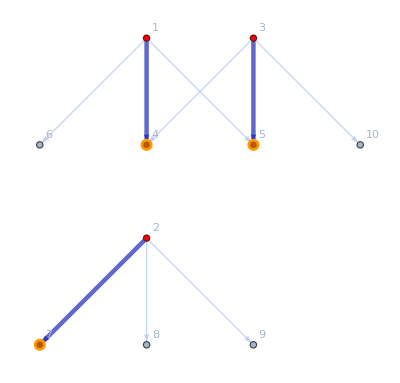

{1->4,2->7,3->5}

```mathematica
(*generalize process. still may need to increase k in some cases, doesn't catch them*)
(*l1 is the list with which you want to extract points that are most representative of that in l2, and l2 are the exact coordinates that we make vertex choices off of.*)
(*sign=1 means you're going (from, to) where you want the vertices in (to).
 for example from the target sites to the actual sites in 2.
 Whereas -1 means you're going (from, to) but you're generating vertices in (from). It could be avoided to split it up this way but it's just how I started doing it. So for sign=-1 an example is you want sites in vertex 1, and you're going from vertex1 verts to the target sites in neuron 2.*)
test2[l1_,l2_,sign_]:=(candpts=ArrayReshape[Flatten[Table[Nearest[l1,l2[[i]],k],{i,Length[l2]}]],{Length[l2]*3,3}];Print[Length[candpts]];coords=Table[r3r1[i,candpts],{i,Length[candpts]}];duppa=Last@Reap[MapIndexed[Sow[#2,#1]&,coords]];duppa=Table[Flatten[duppa[[i]]],{i,Length[duppa]}];relabel3[duppa];unqs=Sort[DeleteDuplicates[rel]];image=Range[Length[unqs]]+Max[rel];h=<|AssociationThread[unqs->image],AssociationThread[image->unqs]|>;targinds=Map[h,rel]-Max[rel];

If[sign==1,(inda=Range[Length[l2]];indb=Join[targinds,targinds,targinds]+Length[l2]),(inda=Join[targinds,targinds,targinds]+Length[l2];indb=Range[Length[l2]])];

verts=Join[l2,DeleteDuplicates[candpts]];

If[sign==1,edges=ArrayReshape[Flatten[Table[Flatten[Transpose@{ConstantArray[inda[[i]],k], indb[[(i-1)*k+1;;i*k]]}],{i,Length[inda]}]],{Length[candpts],2}],edges=ArrayReshape[Flatten[Table[Flatten[Transpose@{inda[[(i-1)*k+1;;i*k]],ConstantArray[indb[[i]],k]}],{i,Length[indb]}]],{Length[candpts],2}]];

edgeweights=Table[EuclideanDistance[verts[[edges[[i]][[1]]]],verts[[edges[[i]][[2]]]]],{i,Length[edges]}];gcon=Graph[DirectedEdge@@@edges,EdgeWeight->edgeweights, VertexStyle->{1|2|3->Red},VertexLabels->"Name"];
GraphPlot[gcon, EdgeLabels->"EdgeWeight"];
supplyDemand=If[#≤Length[l2],1*sign,-1*sign]&/@VertexList[gcon];
FindMinimumCostFlow[gcon,supplyDemand,"OptimumFlowData",EdgeCost->edgeweights])

(*{{1,4},{1,5},{1,6},{2,7},{2,8},{2,9},{3,5},{3,4},{3,10}}*)
edges=ArrayReshape[Flatten[Table[Flatten[Transpose@{inda[[(i-1)*k+1;;i*k]],ConstantArray[indb[[i]],k]}],{i,Length[indb]}]],{Length[candpts],2}]
edgeweights=Table[EuclideanDistance[verts[[edges[[i]][[1]]]],verts[[edges[[i]][[2]]]]],{i,Length[edges]}]
gcon=Graph[DirectedEdge@@@edges,EdgeWeight->edgeweights, VertexStyle->{1|2|3->Red},VertexLabels->"Name"];(*GraphLayout->"BipartiteEmbedding"*)
GraphPlot[gcon, EdgeLabels->"EdgeWeight"]

supplyDemand=If[#≤Length[vertsb],-1,1]&/@VertexList[gcon];
g=FindMinimumCostFlow[gcon,supplyDemand,"OptimumFlowData",EdgeCost->edgeweights];


(*manually create k and rel beforehand*)
k=3
rel=Range[Length[sites12]*3]
f=test2[vf2,sites12]
f["CostValue"](*"EdgeList" "FlowGraph" "FlowMatrix""FlowTable" "FlowValue" "VertexList"*)
f["FlowGraph"]
f["EdgeList"]
```

```mathematica
graph[]:=(inda=Range[Length[sites12]];indb=Join[targinds,targinds,targinds]+Length[sites12];verts=Join[sites12,DeleteDuplicates[candpts]];edges=ArrayReshape[Flatten[Table[Flatten[Transpose@{ConstantArray[inda[[i]],k], indb[[(i-1)*k+1;;i*k]]}],{i,Length[inda]}]],{Length[candpts],2}];edgeweights=Table[EuclideanDistance[verts[[edges[[i]][[1]]]],verts[[edges[[i]][[2]]]]],{i,Length[edges]}];gcon=Graph[DirectedEdge@@@edges,EdgeWeight->edgeweights, VertexStyle->{1|2|3->Red},VertexLabels->"Name"];
GraphPlot[gcon, EdgeLabels->"EdgeWeight"])
```

{1,2,3,4,5,6,7,8,9}

9

{1,2,3,4,5,6,2,1,7}

```mathematica
Print[k, " nearest points on target neuron to each given synapse site"]
candpts=ArrayReshape[Flatten[Table[Nearest[vf2,sites12[[i]],k],{i,Length[sites12]}]],{Length[sites12]*3,3}]
Print["there's ", Length[candpts]- Length[DeleteDuplicates[candpts]], " duplicates" ]
Print["1d candidate points"]
coords=Table[r3r1[i,candpts],{i,Length[candpts]}](*coords, duppa, relabel, then u have the labeled candidate points (not yet adjusted), adjust. Next step would be to make the edges.*)
Print["group duplicates by index of occurrence"]
duppa=Last@Reap[MapIndexed[Sow[#2,#1]&,coords]];(*lump candpts by duplications by index*)
duppa=Table[Flatten[duppa[[i]]],{i,Length[duppa]}]
relabel[duppa,Length[candpts]];
Print["relabeled"]
rel
Print["sorted set"]
unqs=Sort[DeleteDuplicates[rel]]
Print["bijection"]
image=Range[Length[unqs]]+Max[rel](*not really an image since it's not a well-defined function*)
h=<|AssociationThread[unqs->image],AssociationThread[image->unqs]|>;
targinds=Map[h,rel]-Max[rel];
Print["list to target: ", rel, " ", Map[h,rel]-Max[rel]]
```

Set::setps: {1,2,3,4,5,6,7,8,9} in the part assignment is not a symbol.

{1,2,3,4,5,6,7,8,9}

{1,2,3,4,5,6,7,8,9}

3 nearest points on target neuron to each given synapse site

{{682637.,180616.,66643.5},{682731.,180642.,66490.2},{682430.,180621.,66741.5},{682134.,179891.,68275.7},{682217.,179960.,68055.8},{682211.,179914.,68471.7},{682731.,180642.,66490.2},{682637.,180616.,66643.5},{682836.,180645.,66369.}}

there's 2 duplicates

1d candidate points

{000000682637.000000180616.00000066643.5,000000682731.000000180642.00000066490.2,000000682430.000000180621.00000066741.5,000000682134.000000179891.00000068275.7,000000682217.000000179960.00000068055.8,000000682211.000000179914.00000068471.7,000000682731.000000180642.00000066490.2,000000682637.000000180616.00000066643.5,000000682836.000000180645.000000066369.}

group duplicates by index of occurrence

{{1,8},{2,7},{3},{4},{5},{6},{9}}

relabeled

{1,2,3,4,5,6,2,1,9}

sorted set

{1,2,3,4,5,6,9}

bijection

{10,11,12,13,14,15,16}

list to target: {1,2,3,4,5,6,2,1,9} {1,2,3,4,5,6,2,1,7}

```mathematica
(*note that k may have to be increased*)
k=3;
(*So here either I forgot what I was doing or there was more to do. Basically I can find the k nearest neighbors, do a mincost (unfinished). But I have to eventually wire synapse a and b together. So this finds the neurons used for synapse b. I think the idea was that for synaspse a it doesn't matter if multiple ones come in to the same place, so for now I could just do nearest to the result of the mincost and call it good.*)
Print[k, " nearest points on target neuron to each given synapse site"]
candpts=ArrayReshape[Flatten[Table[Nearest[vf2,sites12[[i]],k],{i,Length[sites12]}]],{Length[sites12]*3,3}]
Print["there's ", Length[candpts]- Length[DeleteDuplicates[candpts]], " duplicates" ]
Print["1d candidate points"]
coords=Table[r3r1[i,candpts],{i,Length[candpts]}](*coords, duppa, relabel, then u have the labeled candidate points (not yet adjusted), adjust. Next step would be to make the edges.*)
Print["group duplicates by index of occurrence"]
duppa=Last@Reap[MapIndexed[Sow[#2,#1]&,coords]];(*lump candpts by duplications by index*)
duppa=Table[Flatten[duppa[[i]]],{i,Length[duppa]}]
relabel[duppa,Length[candpts]];
Print["relabeled"]
rel
Print["sorted set"]
unqs=Sort[DeleteDuplicates[rel]]
Print["bijection"]
image=Range[Length[unqs]]+Max[rel](*not really an image since it's not a well-defined function*)
h=<|AssociationThread[unqs->image],AssociationThread[image->unqs]|>;
targinds=Map[h,rel]-Max[rel];
Print["list to target: ", rel, " ", Map[h,rel]-Max[rel]]
```

3 nearest points on target neuron to each given synapse site

{{682637.,180616.,66643.5},{682731.,180642.,66490.2},{682430.,180621.,66741.5},{682134.,179891.,68275.7},{682217.,179960.,68055.8},{682211.,179914.,68471.7},{682731.,180642.,66490.2},{682637.,180616.,66643.5},{682836.,180645.,66369.}}

there's 2 duplicates

1d candidate points

{000000682637.000000180616.00000066643.5,000000682731.000000180642.00000066490.2,000000682430.000000180621.00000066741.5,000000682134.000000179891.00000068275.7,000000682217.000000179960.00000068055.8,000000682211.000000179914.00000068471.7,000000682731.000000180642.00000066490.2,000000682637.000000180616.00000066643.5,000000682836.000000180645.000000066369.}

group duplicates by index of occurrence

{{1,8},{2,7},{3},{4},{5},{6},{9}}

relabeled

{1,2,3,4,5,6,2,1,9}

sorted set

{1,2,3,4,5,6,9}

bijection

{10,11,12,13,14,15,16}

list to target: {1,2,3,4,5,6,2,1,9} {1,2,3,4,5,6,2,1,7}

{1,2,3}

{4,5,6,7,8,9,5,4,10,4,5,6,7,8,9,5,4,10,4,5,6,7,8,9,5,4,10}

{{682732,180668,66720},{682220,180032,68240},{682856,180680,66600},{682637.,180616.,66643.5},{682731.,180642.,66490.2},{682430.,180621.,66741.5},{682134.,179891.,68275.7},{682217.,179960.,68055.8},{682211.,179914.,68471.7},{682836.,180645.,66369.}}

{{1,4},{1,5},{1,6},{2,7},{2,8},{2,9},{3,5},{3,4},{3,10}}

{133.051,231.265,306.391,169.397,198.032,260.152,170.659,232.81,234.491}

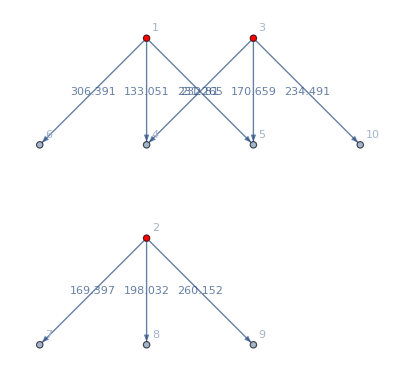

```mathematica
inda=Range[Length[sites12]](*set A indices*)
indb=Join[targinds,targinds,targinds]+Length[sites12](*set B indices*)
verts=Join[sites12,DeleteDuplicates[candpts]]

edges=ArrayReshape[Flatten[Table[Flatten[Transpose@{ConstantArray[inda[[i]],k], indb[[(i-1)*k+1;;i*k]]}],{i,Length[inda]}]],{Length[candpts],2}]
edgeweights=Table[EuclideanDistance[verts[[edges[[i]][[1]]]],verts[[edges[[i]][[2]]]]],{i,Length[edges]}]
gcon=Graph[DirectedEdge@@@edges,EdgeWeight->edgeweights, VertexStyle->{1|2|3->Red},VertexLabels->"Name"];(*GraphLayout->"BipartiteEmbedding"*)
GraphPlot[gcon, EdgeLabels->"EdgeWeight"]
```

```mathematica
(*Do Mincost to determine best pairing*)
(*https://mathematica.stackexchange.com/questions/111576/how-to-get-all-perfect-or-near-perfect-matchings-of-a-graph/112221#112221*)

supplyDemand=If[#≤Length[sites12],1,-1]&/@VertexList[gcon];
f=FindMinimumCostFlow[gcon,supplyDemand,"OptimumFlowData",EdgeCost->edgeweights];

f["CostValue"](*"EdgeList" "FlowGraph" "FlowMatrix""FlowTable" "FlowValue" "VertexList"*)
f["FlowGraph"]
f["EdgeList"]
(*cool*)
```

473.107

-Graphics-

{1->4,2->7,3->5}

```mathematica
(*Create composite graph*)
vecomp=Join[ve1,ve2+Length[vf1]]
(*ve3+ Length[vf1]+Length[vf2]]*)
vfcomp=Join[vf1,vf2](*,vf3]*)

p=f["EdgeList"]
currvert=vf2
p[[1]][[2]]
indsb=Flatten[Table[vxi=verts[[p[[i]][[2]]]];Flatten[Position[vfcomp,vxi]],{i,Length[p]}]](*so grab the indices, make edges*)
vertsb=Table[verts[[p[[i]][[2]]]],{i,Length[p]}]
(*vx1=verts[[4]]
vx2=verts[[7]]
vx3=verts[[5]]
Position[vf2,vx1]
Position[vf2,vx2]
Position[vf2,vx3]*)
```

{{2,11},{3,2778},{4,7303},{5,8702},{6,8197},{7,8454},{8,8703},{9,8075},{10,2},{11,15},{12,15},{13,19},{14,10},{15,13},{16,14},{17,16},{18,16},{19,21},{20,13},{21,24},{22,17},{23,20},{24,26},{25,24},{26,29},33519,{33546,33538},{33547,33542},{33548,33541},{33549,33546},{33550,33548},{33551,33548},{33552,33549},{33553,33549},{33554,33562},{33555,33547},{33556,33551},{33557,33559},{33558,33559},{33559,33560},{33560,33555},{33561,33557},{33562,33557},{33563,33553},{33564,33554},{33565,33563},{33566,33556},{33567,33566},{33568,33567},{33569,33568},{33570,33568}}
 |  |  |  |

{{770718.,209327.,161420.},{677431.,176223.,71922.2},{685692.,173747.,87143.},{765299.,199392.,110799.},{767254.,197989.,111555.},{766695.,198537.,110761.},{766990.,199756.,110541.},{767255.,200361.,111024.},33556,{687659.,179438.,74116.},{687677.,182375.,72985.5},{687792.,181853.,74445.},{687841.,181773.,74367.},{687935.,181777.,74322.9},{687981.,181713.,74361.},{688163.,182014.,74060.}}
 |  |  |  |

{1->4,2->7,3->5}

{{655480.,177707.,44284.4},{654291.,179104.,44437.6},{654185.,178862.,44553.7},{653778.,179461.,44649.8},{588116.,174013.,92071.},{655322.,177450.,44098.8},{588147.,173943.,92148.},{588206.,174136.,91992.6},15412,{687682.,182390.,73101.},{687659.,179438.,74116.},{687677.,182375.,72985.5},{687792.,181853.,74445.},{687841.,181773.,74367.},{687935.,181777.,74322.9},{687981.,181713.,74361.},{688163.,182014.,74060.}}
 |  |  |  |

4

{32291,32211,32356}

{{682637.,180616.,66643.5},{682134.,179891.,68275.7},{682731.,180642.,66490.2}}

3 nearest points on target neuron to each given synapse site

{{682837.,180612.,66858.},{682818.,180603.,66875.1},{682789.,180628.,66895.9},{682236.,180326.,68454.4},{682130.,180321.,68496.9},{682242.,180328.,68453.4},{682953.,180649.,66692.1},{682933.,180605.,66731.9},{682921.,180600.,66746.8}}

there's 0 duplicates

1d candidate points

{000000682837.000000180612.000000066858.,000000682818.000000180603.00000066875.1,000000682789.000000180628.00000066895.9,000000682236.000000180326.00000068454.4,000000682130.000000180321.00000068496.9,000000682242.000000180328.00000068453.4,000000682953.000000180649.00000066692.1,000000682933.000000180605.00000066731.9,000000682921.000000180600.00000066746.8}

group duplicates by index of occurrence

{{1},{2},{3},{4},{5},{6},{7},{8},{9}}

relabeled

{1,2,3,4,5,6,7,8,9}

sorted set

{1,2,3,4,5,6,7,8,9}

bijection

{10,11,12,13,14,15,16,17,18}

list to target: {1,2,3,4,5,6,7,8,9} {1,2,3,4,5,6,7,8,9}

{{682732,180668,66720},{682220,180032,68240},{682856,180680,66600},{682837.,180612.,66858.},{682818.,180603.,66875.1},{682789.,180628.,66895.9},{682236.,180326.,68454.4},{682130.,180321.,68496.9},{682242.,180328.,68453.4},{682953.,180649.,66692.1},{682933.,180605.,66731.9},{682921.,180600.,66746.8}}

inda

{4,5,6,7,8,9,10,11,12,4,5,6,7,8,9,10,11,12,4,5,6,7,8,9,10,11,12}

indb

{1,2,3}

verts

{{682637.,180616.,66643.5},{682134.,179891.,68275.7},{682731.,180642.,66490.2},{682837.,180612.,66858.},{682818.,180603.,66875.1},{682789.,180628.,66895.9},{682236.,180326.,68454.4},{682130.,180321.,68496.9},{682242.,180328.,68453.4},{682953.,180649.,66692.1},{682933.,180605.,66731.9},{682921.,180600.,66746.8}}

{{4,1},{5,1},{6,1},{7,2},{8,2},{9,2},{10,3},{11,3},{12,3}}

{293.704,294.51,295.152,481.745,483.69,484.614,300.087,317.255,322.038}

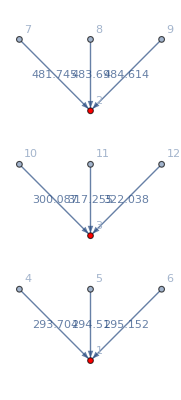

1075.54

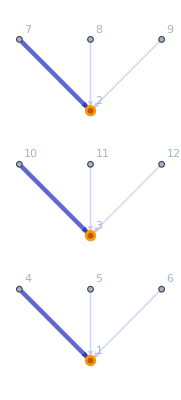

{4->1,7->2,10->3}

{682637.,180616.,66643.5}

{682134.,179891.,68275.7}

{682731.,180642.,66490.2}

{{14148}}

{{14068}}

{{14213}}

```mathematica
(*Next, sew the neurons together*)
(*get the vertices from neuron 1. I think distinct vertices would be good just to emulate distinct synapses, so repeat the process*)

k=3;
Print[k, " nearest points on target neuron to each given synapse site"]
candpts=ArrayReshape[Flatten[Table[Nearest[vf1,vertsb[[i]],k],{i,Length[vertsb]}]],{Length[vertsb]*3,3}]
Print["there's ", Length[candpts]- Length[DeleteDuplicates[candpts]], " duplicates" ]
Print["1d candidate points"]
coords=Table[r3r1[i,candpts],{i,Length[candpts]}](*coords, duppa, relabel, then u have the labeled candidate points (not yet adjusted), adjust. Next step would be to make the edges.*)
Print["group duplicates by index of occurrence"]
duppa=Last@Reap[MapIndexed[Sow[#2,#1]&,coords]];(*lump candpts by duplications by index*)
duppa=Table[Flatten[duppa[[i]]],{i,Length[duppa]}]
relabel[duppa,Length[candpts]];
Print["relabeled"]
rel
Print["sorted set"]
unqs=Sort[DeleteDuplicates[rel]]
Print["bijection"]
image=Range[Length[unqs]]+Max[rel](*not really an image since it's not a well-defined function*)
h=<|AssociationThread[unqs->image],AssociationThread[image->unqs]|>;
targinds=Map[h,rel]-Max[rel];
Print["list to target: ", rel, " ", Map[h,rel]-Max[rel]]

verts=Join[sites12,DeleteDuplicates[candpts]]
Print["inda"]
inda=Join[targinds,targinds,targinds]+Length[vertsb](*set A indices*)
Print["indb"]
indb=Range[Length[vertsb]](*set b, going to neuron b (reversed from sites to targ since it's pre to targ*)
Print["verts"]
verts=Join[vertsb,DeleteDuplicates[candpts]]

(*{{1,4},{1,5},{1,6},{2,7},{2,8},{2,9},{3,5},{3,4},{3,10}}*)
edges=ArrayReshape[Flatten[Table[Flatten[Transpose@{inda[[(i-1)*k+1;;i*k]],ConstantArray[indb[[i]],k]}],{i,Length[indb]}]],{Length[candpts],2}]
edgeweights=Table[EuclideanDistance[verts[[edges[[i]][[1]]]],verts[[edges[[i]][[2]]]]],{i,Length[edges]}]
gcon=Graph[DirectedEdge@@@edges,EdgeWeight->edgeweights, VertexStyle->{1|2|3->Red},VertexLabels->"Name"];(*GraphLayout->"BipartiteEmbedding"*)
GraphPlot[gcon, EdgeLabels->"EdgeWeight"]

supplyDemand=If[#≤Length[vertsb],-1,1]&/@VertexList[gcon];
g=FindMinimumCostFlow[gcon,supplyDemand,"OptimumFlowData",EdgeCost->edgeweights];

g["CostValue"](*"EdgeList" "FlowGraph" "FlowMatrix""FlowTable" "FlowValue" "VertexList"*)
g["FlowGraph"]
g["EdgeList"]
```

{{2,11},{3,2778},{4,7303},{5,8702},{6,8197},{7,8454},{8,8703},{9,8075},{10,2},{11,15},{12,15},{13,19},{14,10},{15,13},{16,14},{17,16},{18,16},{19,21},{20,13},{21,24},{22,17},{23,20},{24,26},{25,24},{26,29},33519,{33546,33538},{33547,33542},{33548,33541},{33549,33546},{33550,33548},{33551,33548},{33552,33549},{33553,33549},{33554,33562},{33555,33547},{33556,33551},{33557,33559},{33558,33559},{33559,33560},{33560,33555},{33561,33557},{33562,33557},{33563,33553},{33564,33554},{33565,33563},{33566,33556},{33567,33566},{33568,33567},{33569,33568},{33570,33568}}
 |  |  |  |

{{770718.,209327.,161420.},{677431.,176223.,71922.2},{685692.,173747.,87143.},{765299.,199392.,110799.},{767254.,197989.,111555.},{766695.,198537.,110761.},{766990.,199756.,110541.},{767255.,200361.,111024.},33556,{687659.,179438.,74116.},{687677.,182375.,72985.5},{687792.,181853.,74445.},{687841.,181773.,74367.},{687935.,181777.,74322.9},{687981.,181713.,74361.},{688163.,182014.,74060.}}
 |  |  |  |

gcomp

{32291,32211,32356}

{{682637.,180616.,66643.5},{682134.,179891.,68275.7},{682731.,180642.,66490.2}}

{4->1,7->2,10->3}

1

{1040,649,1192}

{{682837.,180612.,66858.},{682236.,180326.,68454.4},{682953.,180649.,66692.1}}

{{2,11},{3,2778},{4,7303},{5,8702},{6,8197},{7,8454},{8,8703},{9,8075},{10,2},{11,15},{12,15},{13,19},{14,10},{15,13},{16,14},{17,16},{18,16},{19,21},{20,13},{21,24},{22,17},{23,20},{24,26},{25,24},{26,29},33522,{33546,33538},{33547,33542},{33548,33541},{33549,33546},{33550,33548},{33551,33548},{33552,33549},{33553,33549},{33554,33562},{33555,33547},{33556,33551},{33557,33559},{33558,33559},{33559,33560},{33560,33555},{33561,33557},{33562,33557},{33563,33553},{33564,33554},{33565,33563},{33566,33556},{33567,33566},{33568,33567},{33569,33568},{33570,33568}}
 |  |  |  |

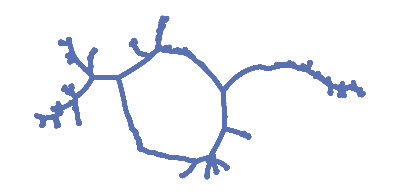

```mathematica
(*Create composite graph*)
vecomp
vfcomp
gcomp
indsb
vertsb

p2=g["EdgeList"]
p2[[1]][[2]]
indsa=Flatten[Table[vxi=verts[[p2[[i]][[1]]]];Flatten[Position[vfcomp,vxi]],{i,Length[p2]}]]
vertsa=Table[verts[[p2[[i]][[1]]]],{i,Length[p]}]

(*either one of these two*)
vecomp=Join[ve1,Transpose@{indsa, indsb}, ve2+Length[vf1]]
gcomp=Graph[vecomp]
GraphPlot[gcomp]
(*vecomp=Join[vecomp, Transpose@{indsa, indsb}]*)
```

```mathematica
g=Graph[ve1]
GraphPlot[g]
```

Graph[{{1,10},{2,2777},{3,7302},{4,8701},{5,8196},{6,8453},{7,8702},{8,8074},{9,1},{10,14},{11,14},{12,18},{13,9},{14,12},{15,13},{16,15},{17,15},{18,20},{19,12},{20,23},{21,16},{22,19},{23,25},{24,23},{25,28},18092,{18118,18119},{18119,18120},{18120,18141},{18121,18109},{18122,18121},{18123,18122},{18124,18100},{18125,18124},{18126,18125},{18127,18126},{18128,18127},{18129,18128},{18130,18131},{18131,18132},{18132,18136},{18133,18123},{18134,18133},{18135,18133},{18136,18138},{18137,18129},{18138,18137},{18139,18142},{18140,18135},{18141,18140},{18142,18140}}]
 |  |  |  |

GraphPlot::graph: A graph object is expected at position 1 in GraphPlot[Graph[{{1,10},{2,2777},{3,7302},{4,8701},{5,8196},{6,8453},{7,8702},{8,8074},{9,1},{10,14},{11,14},{12,18},{13,9},{14,12},{15,13},{16,15},{17,15},{18,20},{19,12},{20,23},{21,16},{22,19},{23,25},{24,23},{25,28},{26,21},{27,26},{28,30},{29,27},{30,31},{31,32},{32,36},{33,29},{34,33},{35,34},{36,37},{37,38},{38,40},{39,41},{40,42},{41,43},{42,39},{43,45},{44,35},{45,47},{46,43},{47,51},{48,44},{49,48},{50,48},«18092»}]].

GraphPlot[Graph[{{1,10},{2,2777},{3,7302},{4,8701},{5,8196},{6,8453},{7,8702},{8,8074},{9,1},{10,14},{11,14},{12,18},{13,9},{14,12},{15,13},{16,15},{17,15},{18,20},{19,12},{20,23},{21,16},{22,19},{23,25},{24,23},{25,28},18093,{18119,18120},{18120,18141},{18121,18109},{18122,18121},{18123,18122},{18124,18100},{18125,18124},{18126,18125},{18127,18126},{18128,18127},{18129,18128},{18130,18131},{18131,18132},{18132,18136},{18133,18123},{18134,18133},{18135,18133},{18136,18138},{18137,18129},{18138,18137},{18139,18142},{18140,18135},{18141,18140},{18142,18140}}]]
 |  |  |  |

```mathematica
leafinds=Flatten[Position[VertexOutDegree[Graph[DirectedEdge@@@ve1]],0]](*Directed edge does take {a,b} to {a->b}*)
ListPointPlot3D[{vf1, vf1[[{1}]], vf2},PlotStyle->{Directive[Green,PointSize[0.002], Opacity[1]],Directive[Red,PointSize[0.015],Opacity[1]],Directive[Green,PointSize[0.002], Opacity[1]]}]
Count[ve1[[;;,1]],leafinds[[1]]](*{11125,11109}*)
Count[ve1[[;;,2]],leafinds[[1]]](*{11127,11125}*)
(*so how is it a leaf index?? It's outdegree should be one according to the edge list..*)
(*Knowing everything has an outdegree of 0 may speed up computations. In-degree doesn't really have a strict limit*)
DeleteDuplicates[VertexOutDegree[Graph[DirectedEdge@@@ve1]]]
(*DeleteDuplicates[VertexOutDegree[Graph[DirectedEdge@@@ve2]]]
DeleteDuplicates[VertexOutDegree[Graph[DirectedEdge@@@ve3]]]*)
(*A couple things: 1) 11125 as a vertex is definitely not a leaf, so however the Graph object is being made does not retain vertex identities OR their identites are not their indices. Find the actual vertex with an outdegree of 0*)
```

{11125}

-Graphics3D-

1

1

{1,0}

{770718.,209327.,161420.}

{770729.,200927.,168483.}

```mathematica
ve1[[11126]]
VertexOutDegree[Graph[DirectedEdge@@@ve1]];(*u know what it is is it's giving back the edge (it's not i still don't know).*)
```

{11127,11125}

```mathematica
(*So index 1 is the leaf node.*)
t=Table[Count[ve1[[;;,1]],i],{i,Length[vf1]}];(*how many times each i appears as a head of an edge. Since i=1 -> 0, vertex 1 is a leaf node. Note to self: when you run fractional outputs, check the *)
DeleteDuplicates[t]
Length[t]
Length[vf1]
t
```

{0,1}

18143

18143

{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,17858,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
 |  |  |  |

```mathematica
Position[ve1,{11114,1}]
(*DirectedEdge @@@ ve1*)
Position[DirectedEdge@@@ve1,11114->1]
Length[VertexOutDegree[Graph[DirectedEdge@@@ve1]]]
VertexOutDegree[Graph[DirectedEdge@@@ve1]][[11113]]
VertexOutDegree[Graph[DirectedEdge@@@ve1]][[11125]](*I'm SO CONFUSED*)
Length[ve1]
Length[vf1]
(*starting to think that the vertex identities are not by index..*)
```

{{11113}}

{{11113}}

18143

1

0

18142

18143

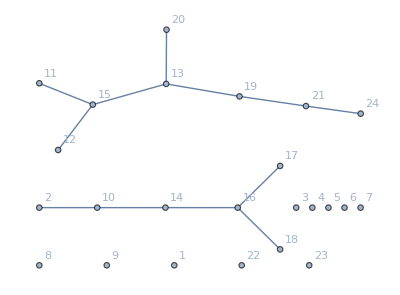

-Graphics-

```mathematica
g=Graph[ve1[[9;;20]],VertexLabels->"Name"]
GraphPlot[g](*So it definitely labels vertices correctly given the edges, either the vertex coordinates don't sync up or something else *)
```

```mathematica
ve1[[1;;20]]
```

{{2,11},{3,2778},{4,7303},{5,8702},{6,8197},{7,8454},{8,8703},{9,8075},{10,2},{11,15},{12,15},{13,19},{14,10},{15,13},{16,14},{17,16},{18,16},{19,21},{20,13},{21,24}}